```mathematica
n=10;
P[c_]:=Module[{adj,leig},
adj=UpperTriangularize[Table[
If[RandomReal[]<c/(n-1),1,0],{i,1,n},{j,1,n}
]
,1];
adj=adj+Transpose[adj];
leig=Sort[N[Eigenvalues[adj],10]]//Last;
1/leig
]
```

```mathematica
data1=Table[P[1],{100}];
data2=Table[P[.5],{100}];
data3=Table[P[1.5],{100}];
```

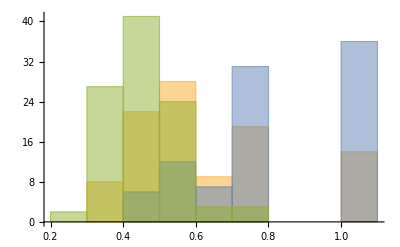

```mathematica
Histogram[{data1,data2,data3}]
```

```mathematica
data=Table[P[c],{100}]/.Table[{c->vals},{vals,{.3,1.}}]
```

```mathematica
Histogram[data]
```

```mathematica
data=Table[Sin[π*RandomReal[]/a],{100}]/.Table[{a->vals},{vals,{2,3,6}}];
Histogram[data]
```